```mathematica
ClearAll["Global`*"]
e0=0;
e=0.05 t;
t=1;
h0:={{e0+e,t},{t,e0-e}};
h1:={{0,0},{t,0}};
hm1:={{0,t},{0,0}};
```

```mathematica
hk=Assuming[k∈Reals,Simplify[Exp[I 2 k](h0+Exp[I 2 k]h1+Exp[-I 2 k]hm1)]]
```

{{0.05 ⅇ^(2 ⅈ k),1+ⅇ^(2 ⅈ k)},{ⅇ^(2 ⅈ k)+ⅇ^(4 ⅈ k),-0.05 ⅇ^(2 ⅈ k)}}

```mathematica
eval=Assuming[k∈Reals,Simplify[Re[Eigenvalues[hk]]]]
```

{-Re[√(1. ⅇ^(2 ⅈ k)+2.0025 ⅇ^(4 ⅈ k)+1. ⅇ^(6 ⅈ k))],Re[√(1. ⅇ^(2 ⅈ k)+2.0025 ⅇ^(4 ⅈ k)+1. ⅇ^(6 ⅈ k))]}

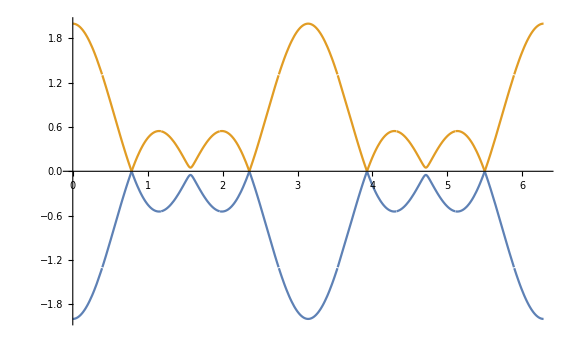

```mathematica
Plot[eval,{k,0,2Pi},ImageSize->Large]
```